### 3D ODE plot

```mathematica
ThreeDyn[T_,X0_,s_,r_,d_,k1_,k2_,k3_,dt_]:=Module[
{dyn,e,ta,c,output},
dyn=NDSolve[
{
e'[t]==s ta[t]-k1 e[t]ta[t]+k2 c[t]-d e[t],
ta'[t]==r ta[t]-k1 e[t]ta[t]+k3 c[t],
c'[t]==k1 e[t] ta[t]-(k2+k3)c[t],
e[0]==X0⟦1⟧,ta[0]==X0⟦2⟧,c[0]==0
},
{e,ta,c},{t,0,T}
,WorkingPrecision->MachinePrecision
];
output={
Table[
{t,Evaluate[e[t]/.dyn]}//Flatten
,{t,0,T,dt}
]
,
Table[
{t,Evaluate[ta[t]/.dyn]}//Flatten
,{t,0,T,dt}
]
,
Table[
{t,Evaluate[c[t]/.dyn]}//Flatten
,{t,0,T,dt}
]
};
{output⟦1⟧,output⟦2⟧,output⟦3⟧}
]
```

### 2D ODE plot

```mathematica
TwoQuasiDyn[T_,X0_,s_,r_,d_,k1_,k2_,k3_,dt_]:=Module[
{dyn,e,ta,output},
dyn=NDSolve[
{
e'[t]==s ta[t]-k1 k3/(k2+k3) e[t]ta[t]-d e[t],
ta'[t]==r ta[t]-k2 k1/(k2+k3) e[t]ta[t],
e[0]==X0⟦1⟧,ta[0]==X0⟦2⟧
},
{e,ta},{t,0,T}
,WorkingPrecision->MachinePrecision
,AccuracyGoal->12
];
output={
Table[
{t,Evaluate[e[t]/.dyn]}//Flatten
,{t,0,T,dt}
]
,
Table[
{t,Evaluate[ta[t]/.dyn]}//Flatten
,{t,0,T,dt}
]
};
{output⟦1⟧,output⟦2⟧}
]
```

### Show plot

```mathematica
r=1;
```

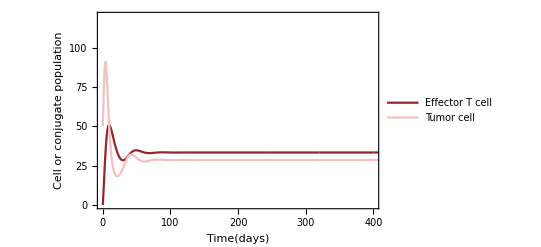

```mathematica
LP1 =ListPlot[
ThreeDyn[800,{20,80},0.15,0.3,0.1,0.01,0.9,0.1,0.01]
,PlotStyle->{ColorData["AvocadoColors"][0.05],ColorData["AvocadoColors"][0.5],ColorData["AvocadoColors"][0.95](*,Darker[Green],{Darker[Green],Dashed}*)}
,PlotLegends->LineLegend[{ColorData["AvocadoColors"][0.05],ColorData["AvocadoColors"][0.5],ColorData["AvocadoColors"][0.95]},{"Effector T cell","Tumor cell","Conjugate"}]
,Frame->{{True,False},{True,False}}
,FrameLabel->{"Time(days)","Cell or conjugate population"}
,FrameStyle->Directive[Black,Thickness[0.002]]
, LabelStyle->Directive[{FontSize->16}, Black,FontFamily->"Arial"]
,Joined->True, PlotRange->{{0,400},{0,120}}
];
LP2=ListPlot[
TwoQuasiDyn[800,{0,50},0.15,0.3,0.1,0.01,0.9,0.1,0.01]
,PlotStyle->{ColorData["CherryTones"][0.15],ColorData["CherryTones"][0.85]}
(*,PlotLegends->Placed[{"Effector T cell","Tumor cell"},Above]*)
,PlotLegends->LineLegend[{ColorData["CherryTones"][0.15],ColorData["CherryTones"][0.85](*,Darker[Green],{Darker[Green],Dashed}*)},{"Effector T cell","Tumor cell"}]
,Frame->{{True,False},{True,False}}
,FrameLabel->{"Time(days)","Cell or conjugate population"}
,FrameStyle->Directive[Black,Thickness[0.002]]
, LabelStyle->Directive[{FontSize->16}, Black,FontFamily->"Arial"]
,Joined->True, PlotRange->{{0,400},{0,120}}
];
Show[LP2(*,LP2*)]
```